# Constants

```mathematica
fullSimplifyReal[x_]:=Assuming[_Symbol ∈ Reals && _Symbol>0, FullSimplify@x]

myFormatConvertToNegativePowers = StandardForm[#/.Power[expr_, r_?Negative] :> Superscript[expr,r] ]&;



CL=2.997925 10^10;
Gr=6.67 10^-8;
ARAD=7.56464 10^(-15);

KPE=0.4;
KPDUST = 10;       (* dust kappa *)

SGT=6.6524 10^-25; (*Thomson cross section cm^2*)
RGAS=8.31 10^7/μm/.μm->1.;
KB=1.38062 10^-16;
PC=3.085678 10^18;
Msol=1.989 10^33;
MBH=10^7 Msol;
MP=1.672661 10^-24;
SGB = ARAD*CL/4;
DAY = 24 3600;
YR=31536000;
MsolYr = Msol/YR;
KM=10^5;

TSUB = 1500;

rulzGlob={α->0.1, ϵ->0.1, η->0.1, κ->10, Subscript[T, s]->T0, M->MBH, Mdtsc -> 0.2 MsolYr};

rulForConst={J->1, m->1,Rg->RGAS, σ->SGB,G->Gr,c->CL, a->ARAD};
```

# Formulas

```mathematica
SchwarzchildRadius[M_] := 2Gr M /CL^2;

KepplerVelocity[M_, r_] := √(Gr M/r);

KepplerTimeScale[M_, r_] :=r/KepplerVelocity[M, r]

EddLum[M_]  := 4 Pi CL Gr M/KPE;
```

```mathematica
MassRange = Msol(10^#&) /@Range[5,9]//N
EddLum[MassRange]
```

{1.989×10^38,1.989×10^39,1.989×10^40,1.989×10^41,1.989×10^42}

{1.24949×10^43,1.24949×10^44,1.24949×10^45,1.24949×10^46,1.24949×10^47}

```mathematica
Solve[KepplerVelocity[MBH m,r]==5000 KMS  ,r]⟦1,1,2⟧
%/SchwarzchildRadius[MBH m]

%%/PC
```

5.30665×10^15 m

1797.51

0.00171977 m

2.95222×10^13

```mathematica
0.01PC/SchwarzchildRadius[MBH]
0.001PC/CL/DAY

KepplerVelocity[MBH, 0.001PC]/10^5
KepplerTimeScale[MBH, 0.1 PC]/YR
```

10452.1

```mathematica
(ARAD T^4/3/ρ)^(1/2)/.{T->1500,ρ->MP 10^11}
```

276256.

## α-disk P_gas>>P_rad solution:

P=P_g+P_r = (ρ R_g T)/μ+(a T^4)/3,

"isothermal" sound speed:  C^2=(R_g T)/μ+(a T^4)/(3ρ)

viscosity:

ν→(C^2 α)/Ω, where   C^2→(R_g T)/m, or   C^2=(R_g T)/μ+(a T^4)/(3ρ).

```mathematica
(* 1. main set of equations *)

EqHoriz = Σ ν -Mdt/(3π) J
EqVertTtau = T^4 - 3/8 κ Σ T04  (* T04 = Subscript[T, 0]^4 *)

EqTempViscDissp =  T04 - 9/(8 σ) Ω^2 ν Σ

EqNu = ν -> α  C^2/Ω/.  C^2-> (Rg T/m) (*+ (b T^4)/(3ρ)/.b->0*)

(*0 rules *)
OmegaRul = Ω->G^(1/2) M^(1/2) r^(-3/2);
```

-(J Mdt)/(3 π)+ν Σ

T^4-(3 T04 κ Σ)/8

T04-(9 ν Σ Ω^2)/(8 σ)

ν→(Rg T α)/(m Ω)

```mathematica
(* 2. main set of equations *)

ClearAll[EqT,EqTsolution,EqS,EqΣsolution,EqTeffsolution,AGasDiskTeffFunc,AGasDiskTempFunc,ADiskΣFunc,Ω,tmp]

EqReduced1 = EqHoriz/.EqNu;
EqReduced2 = EqVertTtau/.EqNu;
EqReduced3 = EqTempViscDissp/.EqNu
EqReduced2 = EqReduced2/.Solve[EqReduced3==0,T04];


(*1  midplane temperature *)
EqT =EqReduced2/.Solve[EqReduced1==0,Σ];
EqTsolution=Solve[EqT==0,T][[2]]
Print["T_c=", TcSolution = EqTsolution⟦1,2⟧]

(*1.1  surface temperature *)
tmp = EqTempViscDissp/.Solve[EqHoriz==0,Σ];
EqTeffsolution=(Solve[tmp==0,T04][[1]][[1]][[2]]/.OmegaRul)^(1/4);

AGasDiskTeffFunc[r_, M_, Mdt_]=EqTeffsolution;

Print["T_s=", TsSolution = AGasDiskTeffFunc[r, M, Mdt]]


(*2  surface density  *) 
EqS= EqReduced1/.EqTsolution;
EqΣsolution = Solve[EqS==0,Σ][[1]]


(* building numerical functions from above results *)
AGasDiskTempFunc[r_, M_, Mdt_] =Assuming[{M>0},EqTsolution[[1]][[2]]/.OmegaRul];
ADiskΣFunc[r_, M_, Mdt_] =EqΣsolution[[1]][[2]]/.OmegaRul;


ClearAll[EqT,EqS,EqTeffsolution,Ω,tmp]
```

T04-(9 Rg T α Σ Ω)/(8 m σ)

{T→((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))}

T_c=((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))

T_s=((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)

{Σ→(2 (2/3)^(1/5) J^(3/5) m^(4/5) Mdt^(3/5) σ^(1/5) Ω^(2/5))/(3 π^(3/5) Rg^(4/5) α^(4/5) κ^(1/5))}

density in the midplane is calculated from

Σ  =  2 H ρ 

and

H→ C/Ω, 

substituting  ν→(C^2 α)/Ω and  C^2= Ω^2 H^2  both to 

EqHoriz = Σ ν -(Ṁ)/(3π) J(R)

```mathematica
CForm[T=((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))]
```

(Power(1.5,0.2)*Power(J,0.4)*Power(m,0.2)*Power(Mdt,0.4)*Power(κ,0.2)*
     Power(Ω,0.6))/(2.*Power(Pi,0.4)*Power(Rg,0.2)*Power(α,0.2)*Power(σ,0.2))

```mathematica
(* 3. finding a disk thickness *)

EqHsolution = EqHoriz/. ν-> α C^2/Ω/. C^2-> (H Ω)^2/.EqΣsolution/.OmegaRul;
EqHsolution = Solve[EqHsolution==0, H][[2]];
Print[" (H)_gas = ",  EqHsolution⟦1,2⟧ ]

EqHsolution = Assuming[r>0, Simplify[EqHsolution[[1]][[2]]/r]];



ADiskH2Rfunc[r_, M_, Mdt_] = EqHsolution/r;

Print[" (H/R)_gas = ", 
ADiskH2Rfunc[r, M, Mdt]]

Print[" (dT/dz)_gas ≂ T_c/h= ", TcSolution/EqHsolution//Simplify ]
```

(H)_gas = (3^(1/10) J^(1/5) Mdt^(1/5) Rg^(2/5) κ^(1/10))/(2^(3/5) m^(2/5) π^(1/5) ((√G √M)/r^(3/2))^(7/10) α^(1/10) σ^(1/10))

(H/R)_gas = (3^(1/10) J^(1/5) Mdt^(1/5) Rg^(2/5) κ^(1/10))/(2^(3/5) m^(2/5) (√G √M)^(7/10) π^(1/5) r^(19/20) α^(1/10) σ^(1/10))

(dT/dz)_gas ≂ T_c/h= (3^(1/10) J^(1/5) m^(3/5) (√G √M)^(7/10) Mdt^(1/5) κ^(1/10) Ω^(3/5))/(2^(3/5) π^(1/5) r^(1/20) Rg^(3/5) α^(1/10) σ^(1/10))

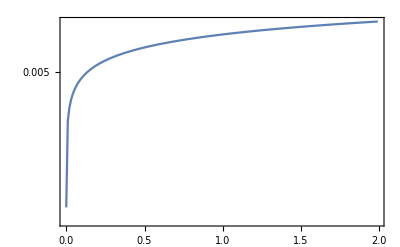

```mathematica
PlotHOverRGasMode = Module[{X1,X2,xmin=0.0001,xmax=2, dx=0.01,rulz, 
			fp1,f1,fp0,f0,Ts,RSubAGN,frsub,T0=1400},
			
rulz={α->0.5, ϵ->0.1, η->0.1, κ->1, Subscript[T, s]->T0, M->MBH, Mdtsc->0.2 MsolYr};

X1 = Range[xmin,xmax,dx];

(* H/R *)
f0[x_]:=ADiskH2Rfunc[x, M, Mdtsc]/.rulForConst/.rulz;

fp0 = MapThread[{#1,#2}&,{X1, f0 /@ (PC X1)}];

ListLogPlot[{fp0},
	PlotStyle->{{Grey}},
	Joined->True,Frame->True,
   PlotLabels->Placed["H/R",Above]
]
]
```

```mathematica
Температура фотосферы:
```

```mathematica
((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)/.rulForConst/.{M->10^7 Subscript[M, 7] Msol, Mdt->0.1MsolYr Subscript[Ṁ, 0.1],r->0.005 Subscript[r, 0.005] PC}
```

```mathematica
1479 ((Subscript[M, 7] Subscript[Ṁ, 0.1])/Subscript[r, 0.005]^3)^(1/4)
```

## DDSR_1 Sublimation radius:

## Disk effective temperature T_eff

```mathematica
AGasDiskTeffFunc[r, M, Mdt]
```

((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)

```mathematica
((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)
```

((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)

## Temperature at the mid - plane

```mathematica
EqTsolution
```

```mathematica
{T->((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))}
```

temperature T_c:

```mathematica
ClearAll[G,r,M,TcFun,x];

TcGasDisk = ((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))/.σ->a c/4;

TcConvectiveDisk = (OneMinB/(3a)Ω c/κ)^(1/4);

Tconv2Tgas  = (TcConvectiveDisk^4/TcGasDisk^4)^(1/4)/.Ω->(G M /r^3)^(1/2)

(*fullSimplifyReal[(TcConvectiveDisk^4/TcGasDisk^4)^(1/4)/.Ω->(G M /r^3)^(1/2)]*)
Assuming[{Ω>0∧J>0∧ m>0∧Mdt>0∧Rg>0∧OneMinB>0∧α>0∧κ>0∧σ>0∧Ω>0 ∧Ts>0 ∧G>0∧ Mdt>0},
FullSimplify[TcConvectiveDisk/TcGasDisk]];



TcFun[r_]:=  ((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω[r]^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5));

(*TcConvectiveDisk[r_]=*)

TcFun[r_]:=  TcFun[r]/.Ω[r]->(G M /r^3)^(1/2);

Assuming[{J≥0∧ m>0∧Mdt>0∧Rg>0∧α>0∧κ>0∧σ>0∧Ω>0 ∧Ts>0 ∧G>0∧ Mdt>0},
Solve[TcFun[x]==Ts,x]
];
```

(2^(4/5) π^(2/5) ((c (a c)^(4/5) OneMinB Rg^(4/5) α^(4/5))/(a J^(8/5) m^(4/5) Mdt^(8/5) ((G M)/r^3)^(7/10) κ^(9/5)))^(1/4))/3^(9/20)

Vertical height in radiation only case :

```mathematica
HeightRad[Mdot_] := 3/(8 Pi) Mdot/c κ


RadOutFun[Mdt_,Tsub_]:=fullSimplifyReal[3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5) ((Rg^(1/5) Ts α^(1/5) σ^(1/5))/(J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5)))^(2/3) σ^(1/5))/(√G J^(2/5) m^(1/5) √M Mdt^(2/5) κ^(1/5)))^(2/3))];

RoutTc=
Assuming[{J≥0∧ m>0∧Mdt>0∧Rg>0∧α>0∧a>0∧κ>0∧σ>0∧Ω>0 ∧Ts>0 ∧G>0∧ Mdt>0},
RadOutFun[Mdt,Tsub]/.{J->1,m->1,σ->a c/4}
]

Print["Rout = ",RoutTc]

Print["H2RatTc =",
H2R = HeightRad[Mdt]/RoutTc]
```

(3^(2/9) (G M)^(1/3) Mdt^(4/9) κ^(2/9))/(2^(8/9) π^(4/9) (a c Rg Ts^5 α)^(2/9))

H2RatTc =(3^(7/9) Mdt^(5/9) (a c Rg Ts^5 α)^(2/9) κ^(7/9))/(4 2^(1/9) c (G M)^(1/3) π^(5/9))

Rout = (3^(2/9) (G M)^(1/3) Mdt^(4/9) κ^(2/9))/(2^(8/9) π^(4/9) (a c Rg Ts^5 α)^(2/9))

Rout = (3^(2/9) (G M)^(1/3) Mdt^(4/9) κ^(2/9))/(2^(8/9) π^(4/9) (a c Rg Ts^5 α)^(2/9))

H2RatTc =(3^(7/9) Mdt^(5/9) (a c Rg Ts^5 α)^(2/9) κ^(7/9))/(4 2^(1/9) c (G M)^(1/3) π^(5/9))

((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))

## Both from above :Temperature in the disk T_c and T_eff:

```mathematica
res= EqTsolution⟦1,2⟧
doubleShow[res]
```

((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))

res

((3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5))/(2 π^(2/5) Rg^(1/5) α^(1/5) σ^(1/5))

## Everything about dust sublimation radii in AD

1.1337×10^45 ϵ_0.1

```mathematica
ClearAll[MdotEdd,MdotEddN]

RSubAGNFun[L_,Ts_]:= (L/(4 π σ Ts^4))^(1/2)/.rulForConst;
RSubAGNFun[0.1 Subscript[ϵ, 0.1] 0.2 MsolYr Mdt02 CL^2,1500]/PC

MdotEdd[r_,κ_]:=4π c r/κ;
MdotEdd[r,κ]

MdotEddN[r_Real,κ_Real] :=MdotEdd[r,κ]/.{c->CL}

RadInFun[Mdt_,Tsub_] := (G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 Tsub^(4/3) σ^(1/3));

RadInFun[Mdt,Tsub]
(*RadInFun[Mdt_Real,Tsub_Real]:=RadInFun[Mdt,Tsub]/.{}*)
(*MdotEddN[1.,2.]*)

MdotEddN[10^13, KPE]
(*Solve[MdotEdd[RadInFun[Mdt,Tsub],κ]==Mdt, Mdt]⟦3,1,2⟧/.rulForConst/.{M -> MBH Subscript[M, 7], Tsub->1500 Subscript[T, 1500], κ->2}
%/MsolYr
*)

Solve[MdotEdd[RadInFun[Mdt,Tsub],κ]==Mdt, Mdt]⟦3,1,2⟧/.rulForConst/.{M -> MBH Subscript[M, 7], Tsub->1500 Subscript[T, 1500], κ->10 Subscript[κ, 10]}
%/MsolYr//myFormatConvertToNegativePowers
```

0.181693 √(Mdt02 ϵ_0.1)

(4 c π r)/κ

(G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 Tsub^(4/3) σ^(1/3))

MdotEddN[10000000000000,0.4]

(5.43138×10^27 √M_7)/(T_1500^2 κ_10^(3/2))

86.1156 √M_7 T_1500^-2 κ_10^(-3/2)

## Eddington mass - accretion rate at the inner radius

Ṁ(R_in)= 86.1156 √M_7 T_1500^-2 κ_10^(-3/2) .
It is also instructive to compare () with (Ṁ)_Edd for electron opacity: (Ṁ)_Edd = 0.13 M_7 at the ISCO:

```mathematica
MdotEdd[3 2G M/c^2,κ]/MsolYr/.{rulForConst}/.{M -> MBH Subscript[M, 7], κ->KPE}
Print["R_ISCO =", 3 SchwarzchildRadius[MBH Subscript[M, 7]]]
```

{0.132255 M_7}

R_ISCO =8.85667×10^12 M_7

(Ṁ)_Edd = 0.13 M_7

(3^(2/9) (G M)^(1/3) Mdt^(4/9) κ^(2/9))/(2 2^(1/3) π^(4/9) (Rg Ts^5 α σ)^(2/9))

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Part::partw: Part 4 of Solve[MdotEdd[(3^(2/9) (G M)^(1/3) (J Mdt)^(4/9) (m κ)^(2/9))/(2 2^(1/3) π^(4/9) (Rg Ts^5 α σ)^(2/9)),κ]==Mdt,Mdt] does not exist.

Solve[MdotEdd[(3^(2/9) (G M)^(1/3) (J Mdt)^(4/9) (m κ)^(2/9))/(2 2^(1/3) π^(4/9) (Rg Ts^5 α σ)^(2/9)),κ]==Mdt,Mdt]⟦4,1,2⟧

```mathematica
MdotEddAtRout
MdotEddAtRout/MsolYr/.{rulForConst}/.{M -> MBH Subscript[M, 7], Ts->1500 Subscript[T, 1500], κ->10 Subscript[κ, 10]}
```

MdotEddAtRout

{1.58552×10^-26 MdotEddAtRout}

```mathematica
(2 2^(1/5) 3^(2/5) c^(9/5) G^(3/5) J^(4/5) m^(2/5) M^(3/5) π)/(Rg^(2/5) Ts^2 α^(2/5) κ^(7/5) σ^(2/5))
```

(2 2^(1/5) 3^(2/5) c^(9/5) G^(3/5) J^(4/5) m^(2/5) M^(3/5) π)/(Rg^(2/5) Ts^2 α^(2/5) κ^(7/5) σ^(2/5))

```mathematica
{(57530.40027064117 Subscript[M, 7]^(3/5))/(α^(2/5) Subscript[T, 1500]^2 Subscript[κ, 10]^(7/5))}
```

{(57530.4 M_7^(3/5))/(α^(2/5) T_1500^2 κ_10^(7/5))}

```mathematica
Mdt (2 2^(1/5) 3^(2/5) c^(9/5) G^(3/5) J^(4/5) m^(2/5) M^(3/5) π)/(Rg^(2/5) Ts^2 α^(2/5) κ^(7/5) σ^(2/5))
```

at outer AD sublimation radius  Ṁ(R_out)=(2 2^(1/5) 3^(2/5) c^(9/5) G^(3/5) J^(4/5) m^(2/5) M^(3/5) π)/(Rg^(2/5) Ts^2 α^(2/5) κ^(7/5) σ^(2/5))

```mathematica
(*RSubAGNFun[] := ((η Ledd)/(4 π σ T0^4))^(1/2)/.Ledd->(4π c G M)/KPE/.rulForConst/.rulz*)
```

## Disk scale - height

Scale height: h≃3/(16π c)Ṁ κ_d

```mathematica
res=3/(16π c)Mdt kpd/.rulForConst/.{Mdt->0.1MsolYr,kpd->50}
res/(0.001PC)
```

6.27811×10^14

```mathematica
z/((z0^2+x^2)^(3/2))/.{z->0.5,z0->0.5, x->1};
```

0.357771

```mathematica
(* ---------- Inner --------- *)

locrulz = {α->0.1, ϵ->0.1, η->0.1, κ->10, Ts->1500 Subscript[T, 1500], M -> MBH Subscript[M, 7], Mdt -> 0.1 MsolYr Subscript[Ṁ, 0.1]};

Rsc= 0.1PC Subscript[r, 0.1];

(4π c G M)/KPE/.locrulz/.rulForConst

Tc = EqTsolution⟦1,2⟧/. Ω -> G^(1/2) M^(1/2) r^(-3/2) /.J->1 /.locrulz/.rulForConst/. r->Rsc


Print["Tsurf=",
 TsurfN = AGasDiskTeffFunc[r, M, Mdt]/. Ω -> G^(1/2) M^(1/2) r^(-3/2)/.J->1/.locrulz/.rulForConst/. r->Rsc//myFormatConvertToNegativePowers
]

res=AGasDiskTeffFunc[r, M, Mdt]/. Ω -> G^(1/2) M^(1/2) r^(-3/2)

Solve[res==Ts, r]

Print["Inner DSR R_in "]
res=Assuming[{J≥0∧ m>0∧Mdt>0∧Rg>0∧α>0∧κ>0∧σ>0∧Ω>0 ∧Ts>0 ∧ Subscript[Ṁ, 0.1]>0},
Solve[res==Ts, r]/.J->1/.locrulz/.rulForConst//myFormatConvertToNegativePowers
]
```

1.24949×10^45 M_7

2075.12 ((√M_7)/(r_0.1^(3/2)))^(3/5) (Ṁ)_0.1^(2/5)

Tsurf=156.483 (M_7 (Ṁ)_0.1 (r_0.1)^-3)^(1/4)

((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)

{{r→-(G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (-3/π)^(1/3))/(2 Ts^(4/3) σ^(1/3))},{r→(G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 Ts^(4/3) σ^(1/3))},{r→((-1)^(2/3) G^(1/3) J^(1/3) M^(1/3) Mdt^(1/3) (3/π)^(1/3))/(2 Ts^(4/3) σ^(1/3))}}

Inner DSR R_in

{{r→(-7.57685×10^15-1.31235×10^16 ⅈ) M_7^(1/3) (Ṁ)_0.1^(1/3) T_1500^(-4/3)},{r→1.51537×10^16 M_7^(1/3) (Ṁ)_0.1^(1/3) T_1500^(-4/3)},{r→(-7.57685×10^15+1.31235×10^16 ⅈ) M_7^(1/3) (Ṁ)_0.1^(1/3) T_1500^(-4/3)}}

```mathematica
1.5153700687716352*10^16 Subscript[M, 7]^(1/3) Subscript[Ṁ, 0.1]^(1/3) Subscript[T, 1500]^(-4/3)/PC
```

0.00491098 M_7^(1/3) (Ṁ)_0.1^(1/3) T_1500^(-4/3)

```mathematica
locrulz = {α->0.1, ϵ->0.1, η->0.1, κ->10, Ts->1500 Subscript[T, 1500], M -> MBH Subscript[M, 7], Mdt -> 0.1 MsolYr Subscript[Ṁ, 0.1]};

(* ---------- Outer --------- *)
 
(*/.Mdt->Ṁ *)

EqTsolution⟦1,2⟧//myFormatConvertToNegativePowers

Tc1 = EqTsolution⟦1,2⟧/. Ω -> G^(1/2) M^(1/2) r^(-3/2);

fullSimplifyReal[Solve[Tc1==Ts, r]⟦1,1,2⟧]//myFormatConvertToNegativePowers

res=Assuming[{J≥0∧ m>0∧Mdt>0∧Rg>0∧α>0∧κ>0∧σ>0∧Ω>0 ∧Ts>0 ∧ Subscript[Ṁ, 0.1]>0},
Solve[Tc1==Ts, r](*/.Mdt->Ṁ *)
]⟦1,1,2⟧

(*Rin = res;
Solve[res
*)
res=res/.locrulz/.rulForConst;

Print["R_out=",
res/PC//FullSimplify//myFormatConvertToNegativePowers
]

ClearAll[locrulz,Tsurf ,Tc,Tc1,res,Rsc, Rin]
```

1/2 (3/2)^(1/5) J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5) Ω^(3/5) π^(-2/5) Rg^(-1/5) α^(-1/5) σ^(-1/5)

1/2 3^(2/9) 2^(-1/3) π^(-4/9) ((((Rg^(1/5) Ts α^(1/5) σ^(1/5))/(J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5)))^(5/3))/(√G √M))^(-2/3)

3^(2/9)/(2 2^(1/3) π^(4/9) ((Rg^(1/5) Ts α^(1/5) ((Rg^(1/5) Ts α^(1/5) σ^(1/5))/(J^(2/5) m^(1/5) Mdt^(2/5) κ^(1/5)))^(2/3) σ^(1/5))/(√G J^(2/5) m^(1/5) √M Mdt^(2/5) κ^(1/5)))^(2/3))

R_out=0.143421 (((T_1500/((Ṁ)_0.1^(2/5)))^(5/3))/(√M_7))^(-2/3)

```mathematica
4π r c/κ/MsolYr/.{r->0.001PC, κ-> 10, c->CL}
```

1.84312

```mathematica
1.5153700687716352 10^16/PC
```

0.00491098

## Various disk properties in one place

```mathematica
ADCalculator := Module[{Rc, Rs, Tc, Tsurf, locrulz,rsc},
	locrulz = {α->0.1, ϵ->0.1, η->0.1, κ->10, Ts->1500 Subscript[T, 1500], M -> MBH Subscript[M, 7], Mdt -> 0.1 MsolYr Subscript[Mdot, 0.1]};
	
	(*MdotNumber[μ_, rulz_] := μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rulz;*)
	
	Tc = EqTsolution/. Ω -> G^(1/2) M^(1/2) r^(-3/2) /.J->1 //Last;
	
	
	Tsurf = AGasDiskTeffFunc[r, M, Mdt]/. Ω -> G^(1/2) M^(1/2) r^(-3/2);(*/.J->1/.locrulz;*)
	
    (*Print["T= ", Tc⟦2⟧, "\n", "Tsurf =", Tsurf[[2]] ];*)
	
	(* [Tc](*/.rulForConst*)*)
	
	Assuming[ Mdt>0 && T>0 && Ts>0 && Rg>0 && α>0 && κ>0 && Σ>0 && 
			Ω>0 && m>0 && σ>0 && J>0 && Mdt>0 && π>0 && M>0,
			
		Rc = Solve[ Tc⟦2⟧ == Ts , r]/.rulForConst;
		
		Rs = Solve[ Tsurf == Ts , r]/.rulForConst;
		
		Rs = Rs/.locrulz;
		
		Print["Rs=", Rs[[2]][[1]][[2]]/PC];
		
	];
	
	Print["R_(sub, c) = ",
		Assuming[Subscript[T, 1500]>0 && Subscript[M, 7]>0,
			Rc = fullSimplifyReal[Part[fullSimplifyReal[Rc/.locrulz],1,1,2]]
		]
		
	];
		Rc
	]

(*Rsubc/PC
Rsubc/CL/DAY
*)
```

Rs={{r→-((0.025989+0.0450143 ⅈ) M^(1/3) Mdt^(1/3))/Ts^(4/3)},{r→(0.051978 M^(1/3) Mdt^(1/3))/Ts^(4/3)},{r→-((0.025989-0.0450143 ⅈ) M^(1/3) Mdt^(1/3))/Ts^(4/3)}}

R_(sub, c) = (4.4255×10^17 M_7^(1/3) Mdot_0.1^(4/9))/T_1500^(10/9)

(0.143421 M_7^(1/3) Mdot_0.1^(4/9))/T_1500^(10/9)

Tsurf =(3/π)^(1/4)

Rs={{r→-((0.025989+0.0450143 ⅈ) M^(1/3) Mdt^(1/3))/Ts^(4/3)},{r→(0.051978 M^(1/3) Mdt^(1/3))/Ts^(4/3)},{r→-((0.025989-0.0450143 ⅈ) M^(1/3) Mdt^(1/3))/Ts^(4/3)}}

R_(sub, c) = (4.4255×10^17 M_7^(1/3) Mdot_0.1^(4/9))/T_1500^(10/9)

(170.855 M_7^(1/3) Mdot_0.1^(4/9))/T_1500^(10/9)

The time scale at outer disk sublimation raius is   

τ=170.855 M_7^(1/3) Mdot_0.1^(4/9)  T_1500^(-10/9) days;

R_(sub,c)=(4.4255×10^17 M_7^(1/3) Mdot_0.1^(4/9))/T_1500^(10/9) ~0.14 pc

```mathematica
α-disk general case of Subscript[P, gas],Subscript[P, rad] :
```

Replace ρ everywhere, using 
					ρ =Σ/(2 H)

ν=(α ((Rg T)/m+(2 b H T^4)/(3 Σ)))/Ω
substituting ν→(C_b^2 α)/Ω where
								C_b^2=((Rg T)/m+(2 b H T^4)/(3 Σ))
and
										C_tot^2= Ω^2 H^2 
both to, C_b needs not to be equal C_tot

unknowns: T, Σ, H

b measures the dependence of ν on P_rad; 
										H=C_tot/Ω is due to dependence of the scaleheight on P_rad

```mathematica
"1. main set of equations:"

Print["EqHoriz = ", EqHoriz = Σ ν -Mdt/(3π) J]
Print["EqVertTtau = ", EqVertTtau = T^4 - 3/8 κ Σ T04 ]

Print["EqTempViscDissp =  ", EqTempViscDissp =  T04 - 9/(8 σ) Ω^2 ν Σ ]

Print["EqNu = ", EqNu = ν - α  C^2/Ω/.  C^2-> (Rg T/m) + (b T^4)/(3ρ) /. ρ->Σ/(2H) ]

OmegaRul = Ω->G^(1/2) M^(1/2) r^(-3/2);
```

1. main set of equations:

EqHoriz = -(J Mdt)/(3 π)+ν Σ

EqVertTtau = T^4-(3 T04 κ Σ)/8

EqTempViscDissp =  T04-(9 ν Σ Ω^2)/(8 σ)

EqNu = ν-(α ((Rg T)/m+(2 b H T^4)/(3 Σ)))/Ω

```mathematica
Module[{tmp},
 
EqTempViscDissp;
tmp = Flatten@Solve[EqHoriz==0,ν];
tmp⟦1,2⟧
]
```

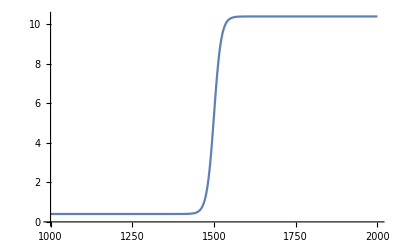

```mathematica
NKappa[t_]:= Block[ {Ts=TSUB, ΔT=11},
			KPE+KPDUST(1+ Exp[-(t-Ts )/ΔT])^-1];

Plot[NKappa[T], {T,1000,2000}]
```

```mathematica
ClearAll[RADiskTempFunc,EqH2rrho,tmp,EqT,tmpNu,EqΣtmp,EqHtmp,RADiskTempEq,EqΣFuncAlg,
tmpScale,RADiskTempEq,r,RADiskTempFunc1];

EqH = H^2 - Subscript[C^2, tot]/Ω^2 /.Subscript[C^2, tot]-> ((Rg T/m) + (a T^4)/(3ρ) ) /.ρ->Σ/(2H); (* note a /= b *)

tmpNu = Solve[EqHoriz==0, ν];

EqReduced2 = EqVertTtau/.Solve[EqTempViscDissp==0, T04]
(*1*)
EqReduced2=EqReduced2/.tmpNu;
EqΣtmp = Solve[EqReduced2==0,Σ]

(*2*)
EqNu/.tmpNu/.EqΣtmp
EqHtmp= Solve[%==0,H]⟦1⟧
EqHtmp/. {Mdt->SuperPlus[F] 8 π/3 Ω^-2 ,σ->a c/4,J->1,m->1,b->a}//FullSimplify

(*2.1*)

EqΣFuncAlg[x_, Temp_] := Module[{res}, res= EqΣtmp⟦1⟧⟦1⟧⟦2⟧/.OmegaRul; res/.{T->Temp, r->x} ]

(*3*)
RADiskTempEq=EqH/.EqΣtmp/.EqHtmp/.OmegaRul//Together//Numerator;

MaxPowTc = 10;
TcReduced = RADiskTempEq⟦1⟧(*/Coefficient[RADiskTempEq⟦1⟧,T,MaxPowTc]*)/.b->a;

Print["Equation for T_c: 0 = ",
Assuming[{π >0 ∧ r>0 ∧ Rg>0 ∧ α>0 ∧ σ>0}, fullSimplifyReal[Cancel[RADiskTempEq⟦1⟧]]]]

Print["Equation for, simplified T_c: 0 = ", Assuming[{π >0 ∧ r>0 ∧ Rg>0 ∧ α>0 ∧ σ>0}, fullSimplifyReal[Cancel[TcReduced]]]]

(*Block[ {$Assumptions = π >0 ∧ r>0 ∧ Rg>0 ∧ α>0 ∧ σ>0}, 
		fullSimplifyReal[Cancel[TcReduced]];
		Print["TcReduced=",TcReduced]]
*)


ClearAll[TcReduced,MaxPowTc]

tmpSc =Coefficient[RADiskTempEq[[1]],T,0];

RADiskTempEq = RADiskTempEq[[1]]/tmpSc//Cancel


RADiskTempFunc1[x_,rulz_] := Module[{solT,fun,tmp},
	tmp=RADiskTempEq/.rulForConst/.rulz//Expand;
	solT = tmp/.Mdt->Mdtsc/.a->ARAD/.b->ARAD;
	solT = solT/.rulz/.r->x;
		
	solT=NSolve[solT == 0 && T>0, T, Reals][[1]][[1]][[2]];
	(*Print["solT=", solT];*)
	solT
]

RADiskSurfTempEq = Solve[Evaluate[EqTempViscDissp/.Solve[EqHoriz==0,ν ][[1]]] == 0, T04]⟦1,1,2⟧/.
					OmegaRul(*/.r->x/.rulez/.Mdt->Mdtsc/.rulForConst*);


ClearAll[RADiskSurfTempFun]
RADiskSurfTempFun[x_,rul_, mdt_] := (RADiskSurfTempEq/.r->x/.rul/.Mdt->mdt/.rulForConst)^(1/4);

(*RADiskSurfTempEq[x_,rulez_] := Module[{solT},*)
(*Print["Tc==",
RADiskTempFunc1[0.01PC, {α->0.1, ϵ->0.1, κ->1, Subscript[T, s]->T0, M->MBH, Mdtsc->0.2 MsolYr}], "\n", ]
*)				

Module[{xmin=0.0001,xmax=2,T0=TSUB, rulz},
	rulz={α->0.1, ϵ->0.1, η->0.1, κ->10, Subscript[T, s]->T0, M->MBH, Mdtsc->0.2 MsolYr};
    LogLogPlot[RADiskTempFunc1[x PC, rulz], {x, xmin, xmax}, PlotLabel->"Disk Temperature"]
]




Print[  "  **************  Step Done **************  "  ]
```

{T^4-(27 κ ν Σ^2 Ω^2)/(64 σ)}

{{Σ→(64 π T^4 σ)/(9 J Mdt κ Ω^2)}}

{{(3 J^2 Mdt^2 κ Ω^2)/(64 π^2 T^4 σ)-(α ((Rg T)/m+(3 b H J Mdt κ Ω^2)/(32 π σ)))/Ω}}

{H→(-64 π^2 Rg T^5 α σ+3 J^2 m Mdt^2 κ Ω^3)/(6 b J m Mdt π T^4 α κ Ω^2)}

{H→-(c Rg T)/(κ F^+)+(4 F^+)/(3 a T^4 α Ω)}

Equation for T_c: 0 = fullSimplifyReal[-27 a b G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+144 G^3 J^4 m^2 M^3 Mdt^4 κ^2 σ+576 a b G J^2 m M Mdt^2 π^2 r^6 Rg T^9 α^2 κ^2 σ-576 b^2 G J^2 m M Mdt^2 π^2 r^6 Rg T^9 α^2 κ^2 σ-6144 G^(3/2) J^2 m M^(3/2) Mdt^2 π^2 r^(9/2) Rg T^5 α κ σ^2+65536 π^4 r^9 Rg^2 T^10 α^2 σ^3]

Equation for, simplified T_c: 0 = fullSimplifyReal[-27 a^2 G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+144 G^3 J^4 m^2 M^3 Mdt^4 κ^2 σ-6144 G^(3/2) J^2 m M^(3/2) Mdt^2 π^2 r^(9/2) Rg T^5 α κ σ^2+65536 π^4 r^9 Rg^2 T^10 α^2 σ^3]

(-27 a b G^(5/2) J^4 m^2 M^(5/2) Mdt^4 r^(3/2) T^4 α κ^3+144 G^3 J^4 m^2 M^3 Mdt^4 κ^2 σ+576 a b G J^2 m M Mdt^2 π^2 r^6 Rg T^9 α^2 κ^2 σ-576 b^2 G J^2 m M Mdt^2 π^2 r^6 Rg T^9 α^2 κ^2 σ-6144 G^(3/2) J^2 m M^(3/2) Mdt^2 π^2 r^(9/2) Rg T^5 α κ σ^2+65536 π^4 r^9 Rg^2 T^10 α^2 σ^3)/(144 G^3 J^4 m^2 M^3 Mdt^4 κ^2 σ)

ReplaceAll::reps: {rulForConst} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

**************  Step Done **************

Disk aspect ratio in general case

Disk aspect ratio in general case:

{H→((√G J √M Mdt)/(2 π r^(3/2) T^4 α)-(32 π r^3 Rg T σ)/(3 G J m M Mdt κ))/b}

{H→((√G J √M Mdt)/(2 π r^(3/2) T^4 α)-(32 π r^3 Rg T σ)/(3 G J m M Mdt κ))/b}

H=1.23678×10^16

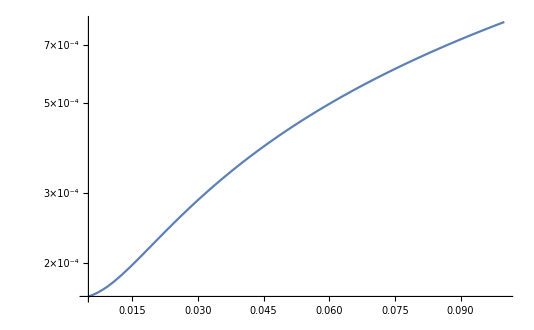

T=405.443

H=9.68267×10^15

res

```mathematica
"Disk aspect ratio in general case: "

ClearAll[ARadDiskHeightfunc]

EqHtmp

EqHtmp=EqHtmp/.OmegaRul//Simplify

ARadDiskHeightfunc[x_, rulz_] := Module[{solH,solT, fun, tmpH},
	tmpT = RADiskTempFunc1[x,rulz];
	(*Print["T=",tmpT];*)
	tmpH = EqHtmp/.OmegaRul/.b->ARAD/.Mdt->Mdtsc/.rulForConst/.rulz/.r->x/.T->tmpT;
	tmpH = tmpH[[1]][[2]]
]


Block[{rulz={ α->0.1, ϵ->0.1, η->0.1, κ->10, Subscript[T, s]->1500, M->MBH, Mdtsc->0.2 MsolYr}},
	Print["H=", ARadDiskHeightfunc[0.5PC, rulz]]]

Block[{rulz={ α->0.1, ϵ->0.1, η->0.1, κ->10, Subscript[T, s]->T0, M->MBH, Mdtsc->0.2 MsolYr}},
		(*ARadDiskHeightfunc[ PC, rulz]*)
		
		(*  uncomment below to plot *)
		LogPlot[ ARadDiskHeightfunc[x PC, rulz]/PC, 
		
		{x, 0.005, 0.1}, PlotLabels->Placed["H/R",{Above}]]
		
		(*Plot3D[ Sin[x y],  {x,0,3},  {y,0,3} ]*)
		
	]
```

Disk midplane density: ρ=Σ/(2H)

```mathematica
fullSimplifyReal[(-64 π^2 Rg T^5 α σ+3 J^2 m Mdt^2 κ Ω^3)/(6 b J m Mdt π T^4 α κ Ω^2)/.b->a]
```

(-(32 π Rg T σ)/(3 J m Mdt κ Ω^2)+(J Mdt Ω)/(2 π T^4 α))/a

```mathematica
EqΣFunc[x_, T_, rulz_] := Block[{},
	EqΣFuncAlg[x,T]/.Mdt->Mdtsc/.rulz/.rulForConst ]

RADiskNdensFunc[x_,rulz_] := Module[ {H, nden,Σ,T},
	T = RADiskTempFunc1[x,rulz];
	Σ = EqΣFunc[x, T, rulz];
	H = ARadDiskHeightfunc[x, rulz];
    nden = Σ/(2 H)/MP
    ];
  
(*RADiskNdensFunc[x, rulzGlob]  
*)
```

```mathematica
ClearAll[pltPrad,pltPgas,pltNdens,pltTemp]  
MdotNumber[μ_, rulz_] := μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rulz;

tmp = Module[{xmin=0.01,xmax=1, 
			T0=TSUB, tmp, rulz,Tgas,pltPrad,pltPgas,pltNdens,pltTemp,RSubAGN,l1,ymin,ymax,μ,Prad,Pgas},
	
	rulz={α->0.1, ϵ->0.1, η->0.1, κ->10, Subscript[T, s]->T0, M-> MBH, Mdtsc -> 0.02 MsolYr};
	
	μ = 10;
	
	Print["Mdot = ", MdotNumber[μ, rulz]/MsolYr];
	(*AppendTo[rulz, Mdtsc->MdotNumber[μ, rulz]];*)
	
	RSubAGN = ((η Ledd)/(4 π σ T0^4))^(1/2)/.Ledd->(4π c G M)/KPE/.rulForConst/.rulz;
	Print["RSubAGN/PC = ", RSubAGN/PC];
	
	Tgas[x_] := AGasDiskTempFunc[x, M, Mdtsc]/.rulForConst/.rulz;
	
	Print[
	Solve[Tgas[x Pc] == 10^5,x]
	];
	
	Prad[x_, rulz_] := (ARAD/3) (RADiskTempFunc1[x,rulz])^4 ;
	
	Pgas[x_, rulz_] := MP RGAS RADiskNdensFunc[x,rulz] RADiskTempFunc1[x,rulz];
	
	pltPrad = LogPlot[ Prad[x PC, rulz], {x, xmin, xmax}, PlotLabel->"Disk P_r(erg cm^-3)", Frame->True];
	
	pltPgas = LogPlot[ Pgas[x PC, rulz] / Prad[x PC, rulz], 
				{x, xmin, xmax}, PlotLabel->"Disk P_g/P_r", Frame->True];
    
    pltNdens = LogLogPlot[RADiskNdensFunc[x PC, rulz], {x, xmin, xmax}, PlotLabel->"Disk n(cm^-3)", Frame->True];
    
    pltTemp  = LogPlot[ {T0, Tgas[PC x], RADiskTempFunc1[PC x,rulz]}, {x, xmin, xmax},
    PlotLabel->"Disk T_c(K)", Frame->True, 
    PlotLegends->Placed[ {"T_sub","T_(c, g)","T_c"}, {Top, Center}]
    ];
    
    
    tmp=FilterRules[AbsoluteOptions[pltTemp], PlotRange];    
    ymin= tmp[[1]][[2]][[1]][[2]];   
    ymax = tmp[[1]][[2]][[2]][[2]];   
    
    l1=Graphics[{Dashed,Line[{{ Log@(RSubAGN/PC), Log@180}, {Log@(RSubAGN/PC), ymax}}]}];
    pltTemp=Show[pltTemp, l1];
    
    
    pltTemp=Rasterize[GraphicsGrid[{{ pltNdens, pltTemp }, {pltPgas, pltPrad}  },ImageSize->Full], ImageResolution->300]
    
    (*Export["/Users/dora/WORK/PROGECTS/SCRIPTS_nb/AccretionSolver/a_disk_four_pan.pdf", pltTemp]*)
    
    
]

ClearAll[rulz]
```

Mdot = 0.220425

RSubAGN/PC = 0.0603189

{{x→(2.03584×10^15)/Pc}}

Ticks::ticks: {Quiet[Charting`ScaledTicks[{Log,Exp}][#1,#2,{6,6}]]&,Charting`ScaledFrameTicks[{Log,Exp}]} is not a valid tick specification.

Ticks::ticks: {Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]} is not a valid tick specification.

Ticks::ticks: {Quiet[Charting`ScaledTicks[{Log,Exp}][#1,#2,{6,6}]]&,Charting`ScaledFrameTicks[{Log,Exp}]} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

-Graphics-

## Single plot:

```mathematica
ClearAll[pltPrad,pltPgas,pltNdens,pltTemp]  
MdotNumber[μ_, rulz_] := μ η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rulz;
```

```mathematica
plotDiskTemp = Module[{xmin=0.001, xmax=2, T0 = TSUB, tmp, Tgas,Tsurf,pltPrad,pltPgas,
					pltNdens,pltTemp,RSubAGN,l1,ymin,ymax,μ,Prad,Pgas,rulz},
	
	rulz={α->0.1, ϵ->0.1, η->0.1, κ->10, Subscript[T, s]->T0, M-> MBH, Mdtsc -> 0.02 MsolYr};
	
	μ=1; (* exess over equilibrium value *)
	
	
	Print["Mdot = ", MdotNumber[μ, rulz]/MsolYr];
	
	(*AppendTo[rulz, Mdtsc->MdotNumber[μ, rulz]];*)
	
	RSubAGN = ((η Ledd)/(4 π σ T0^4))^(1/2)/.Ledd->(4π c G M)/KPE/.rulForConst/.rulz;
	
	Print["RSubAGN/PC = ", RSubAGN/PC];
	
	
	Tsurf[x_] :=RADiskSurfTempFun[x, rulz, Mdtsc]/.rulz;
	
	Print["Tsurf=", RADiskSurfTempFun[x, rulz, Mdtsc]];

    
    pltTemp  = LogLogPlot[ {T0, RADiskTempFunc1[PC x,rulz], Tsurf[PC x]}, {x, xmin, xmax},
              PlotLabel->"Disk Temperature(K)", Frame->False, AxesLabel->{"R(pc)", "T(K)"},
               PlotStyle->{{Blue,Dashed},{Thick},{Thick}}
               (*,PlotLabels->Placed[{"T_SUB=1400"},Automatic]*)
              ];
     
 
    pltTemp = Rasterize[pltTemp, ImageResolution->400]
    
   
   ]
   
  (*Export["/Users/dora/Documents/PROPOSALS/RadDiskTemp.pdf", plotDiskTemp]*)

ClearAll[rulz]
```

Mdot = 0.0220425

RSubAGN/PC = 0.0603189

Tsurf=1.29278×10^9 (Mdtsc/x^3)^(1/4)

-Graphics-

Mdot = 0.0220425

RSubAGN/PC = 135717. √(1/T0^4)

Ticks::ticks: {Quiet[Charting`ScaledTicks[{Log,Exp}][#1,#2,{6,6}]]&,Charting`ScaledFrameTicks[{Log,Exp}]} is not a valid tick specification.

General::stop: Further output of Ticks::ticks will be suppressed during this calculation.

```mathematica
MP Subscript[n, 11] 10^11 RGAS Subscript[T, 100] 1000

ARAD (Subscript[T, 100] 1000)^4
```

0.0138998 n_11 T_100

0.00756464 T_100^4

True Tvir temperature.

P=P_g+P_r = (ρ R_g T)/μ+(a T^4)/3,  

(G M)/r ρ = ρ R_g T+a T^4

```mathematica
TvirNonLin[r_, n_, rulz_]:= Module[{eq, ρ=MP n},
(*finds "virial temperature" from the non-linear equation*)

eq = -(G M)/r ρ + ρ Rg T + a T^4;

eq = eq/.rulForConst/.rulz;

eq=NSolve[eq == 0 && T>0, T, Reals][[1]][[1]][[2]]

]
rulz

LogPlot[ {1500,TvirNonLin[x PC, #, {α->0.5, ϵ->0.1, η->0.1, κ->1, Subscript[T, s]->T0, M->MBH, Mdtsc->0.2 MsolYr}]& /@ {10^7, 10^9, 10^11} }, 
{x, 0.01, 1}, PlotLabel->"Nonlinear Virial Temperature"]
```

rulz

$Aborted

# Plots

```mathematica
AradDistTvir[n_, T_, rulz_]:= Module[{TvirGas,TvirRad,Pr,Pg, ρ=MP n, mum=1},TvirGas=G M/(Rg); Pr=8a T^4/3 ;Pg = ρ Rg T/mum; 
TvirRad=TvirGas (5+8Pr/Pg)^-1/.rulForConst/.rulz
];

AradDistTvir[10^10, T, {α->0.5, ϵ->0.1, η->0.1, κ->1, Subscript[T, s]->T0, M->MBH, Mdtsc->0.2 MsolYr}]
```

(1.59647×10^25)/(5+1.16102×10^-7 T^3)

Mdot = 0.0220425

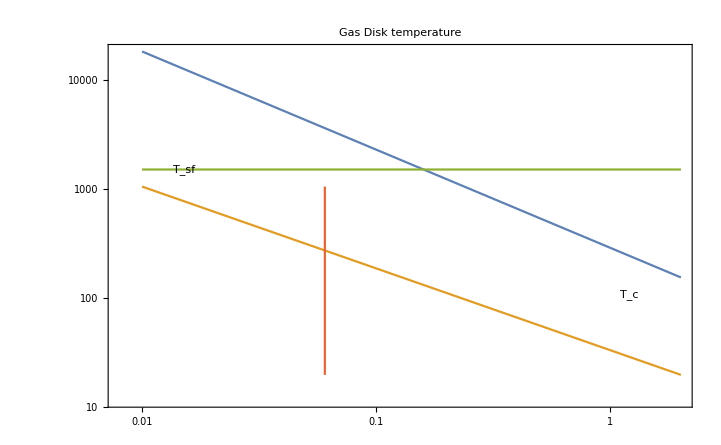

```mathematica
(*plots*)
ClearAll[Mdtsc,rulz]

Module[{X1,X2,X1hrez,xmin=0.01,xmax=2,Nx1=100, Nxhrez=200, rulz, 
			fp1,f1,fp0,f0,Ts, TcDisRad,MdotNumber,
			RSubAGN,frsub,T0=TSUB},
			
rulz={ α->0.1, ϵ->0.1, η->0.1, κ->4, Subscript[T, s]->T0, M->MBH};


MdotNumber[rulz_] := η ϵ^-1 4Pi CL Gr M /KPE/CL^2/.rulz;
		
		
Print["Mdot = ", MdotNumber[rulz]/MsolYr];

(*AppendTo[rulz, Mdtsc->MdotNumber[rulz]];*)
AppendTo[rulz, Mdtsc->0.2MsolYr];

X1 = Range[xmin,xmax,(xmax-xmin)/(Nx1-1)];
X1hrez = Range[xmin,xmax,(xmax-xmin)/(Nxhrez-1)];

(* dust sublimaiton radius *)

RSubAGN = ((η Ledd)/(4 π σ Subscript[T, s]^4))^(1/2)/.Ledd->(4π c G M)/KPE/.rulForConst/.rulz;

f1[x_]:=AGasDiskTempFunc[x, M, Mdtsc]/.rulForConst/.rulz;

f0[x_]:=AGasDiskTeffFunc[x, M, Mdtsc]/.rulForConst/.rulz;

fp0 = f0 /@ (PC X1) ;  (* surface T *)
fp1 = f1 /@ (PC X1) ;  (* equatorial T *)


TcDisRad = MapThread[{#1,#2}&, {X1hrez, RADiskTempFunc1[#,rulz]& /@ (PC X1hrez)}];


Ts = MapThread[{#1,#2}&,{X1, ConstantArray[T0,Length[X1]]}];

X2 = ConstantArray[RSubAGN/PC, Length[X1]];

frsub = MapThread[{#1,#2}&,{X2, fp0}]; (* R_sub_AGN *)

fp0=MapThread[{#1,#2}&,{X1, fp0}];
fp1=MapThread[{#1,#2}&,{X1, fp1}];

(* reference Temperature *)
(*AradDistTvir[ρ_, T_, rulz_];*)



ListLogLogPlot[{fp1,fp0,Ts,frsub},

	(*PlotStyle->{ {Red}, {Grey}, {Orange,DotDashed}, {Black,Dashed}, {Green}},*)
	
	Joined->True,Frame->True,
	PlotLabel->"Gas Disk temperature",
    
    PlotLabels->Placed[{"T_c","T_sf"},{Scaled[1],Left}]
    
	(*PlotLabels->Placed["T_c",Above]*)
	]
]
```

```mathematica
5 10^-3 PC MP 5 10^11 0.4
```

5161.29

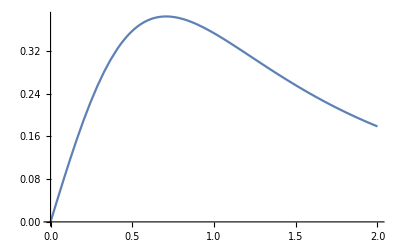

-1/(√(r^2+z^2))

```mathematica
Plot[z/((1+z^2)^(3/2)),{z,0,2}]
Integrate[z/((r^2+z^2)^(3/2)),z]
```

## Separate Functions

## Surface temperature

```mathematica
Ts[r_,Mdt_] := ((3/π)^(1/4) ((G J M Mdt)/(r^3 σ))^(1/4))/2^(3/4)/.{G->Gr,σ->SGB,M->MBH,J->1}

Ts[0.005PC,0.1MsolYr]

Ts[0.01PC,0.1MsolYr]
```

1479.93

879.969